```mathematica
deck = Tuples[{{2,3,4,5,6,7,8,9,10, "J","Q","K","A"},{"♡","♣","♠","♢"}}]
```

{{2,♡},{2,♣},{2,♠},{2,♢},{3,♡},{3,♣},{3,♠},{3,♢},{4,♡},{4,♣},{4,♠},{4,♢},{5,♡},{5,♣},{5,♠},{5,♢},{6,♡},{6,♣},{6,♠},{6,♢},{7,♡},{7,♣},{7,♠},{7,♢},{8,♡},{8,♣},{8,♠},{8,♢},{9,♡},{9,♣},{9,♠},{9,♢},{10,♡},{10,♣},{10,♠},{10,♢},{J,♡},{J,♣},{J,♠},{J,♢},{Q,♡},{Q,♣},{Q,♠},{Q,♢},{K,♡},{K,♣},{K,♠},{K,♢},{A,♡},{A,♣},{A,♠},{A,♢}}

{0.0009,0.0012,0.001,0.001,0.0013,0.0012,0.0013,0.0017,0.0014,0.0016,0.0008,0.002,0.0013,0.0017,0.0018,0.0017,0.0018,0.0011,0.0015,0.0013,0.0014,0.0021,0.001,0.0015,0.0019,0.0013,0.0008,0.001,0.0012,0.0017,0.0021,0.0014,0.0012,0.0009,0.0018,0.0011,0.0018,0.0019,0.0016,0.0014,0.0016,0.0017,0.0015,0.0021,0.0014,0.0014,0.0014,0.0014,0.0013,0.0017,0.0015,0.0017,0.0014,0.0018,0.0012,0.0018,0.0006,0.0013,0.0015,0.0014,0.0015,0.0016,0.0018,0.0018,0.0011,0.0011,0.0015,0.0019,0.0014,0.0015,0.0018,0.001,0.0014,0.002,0.0008,0.0008,0.0014,0.0017,0.0014,0.0017,0.0025,0.0013,0.0011,0.0012,0.0012,0.0013,0.0015,0.0017,0.0016,0.0014,0.0019,0.0014,0.0016,0.0009,0.0017,0.0017,0.0014,0.0017,0.001,0.0017}

0.001454

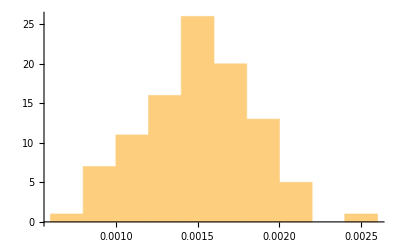

```mathematica
numHands = 10000;
  numSims = 100;
  IsFullHouse[x_]:= If[MemberQ[x,3] && MemberQ[x,2], 1,0]
  
  fullHouseProbs = Table[
  numFullHouses = 0;
Do[
          hand = RandomSample[deck,5];
                 cards = hand[[All,1]];
                 counts = Counts[cards]; 
         vals = Values[counts];
        numFullHouses += IsFullHouse[vals]
     ,numHands
 ];
    N[numFullHouses/numHands]
 ,numSims
]
Mean[fullHouseProbs]
Histogram[fullHouseProbs]
```

```mathematica
calcProb  = N[(Binomial[13,1]*Binomial[4,3]*Binomial[12,1]*Binomial[4,2])/Binomial[52,5]]
```

0.00144058

0.144058